```mathematica
f[x_]:=Module[
{},
E^x
]
Subscript[h, 1]=1 ;
Subscript[h, 2]=0.001;
Subscript[h, 3]=10^-15;

h={Subscript[h, 1], Subscript[h, 2], Subscript[h, 3]};
(* Разлика напред *)
frontD[f_,t_, h_]:=Module[
{},
(f[t+h]-f[t])/h
]
(* Разлика назад *)
backD[f_,t_ , h_]:=Module[
{},
(f[t]-f[t-h])/h
]
(* Централна разлика *)
centralD[f_,t_ , h_]:=Module[
{},
(f[t+h]-f[t-h])/(2h)
]
```

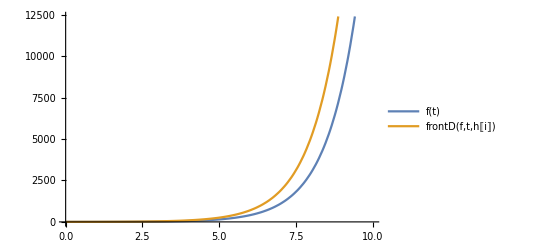
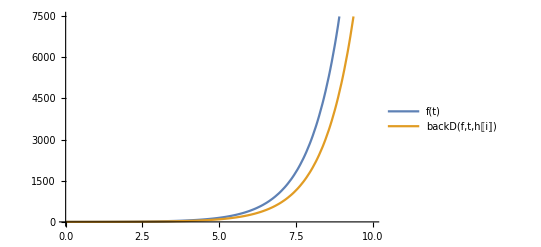
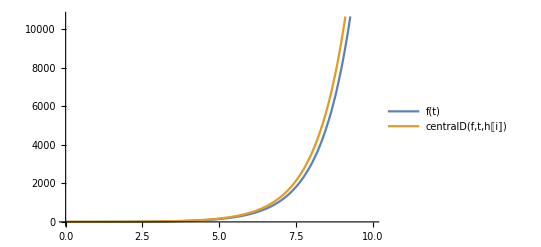
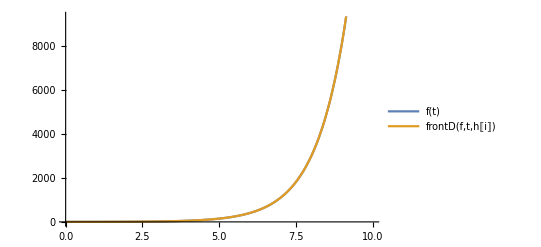
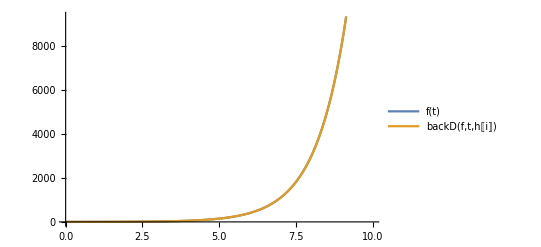
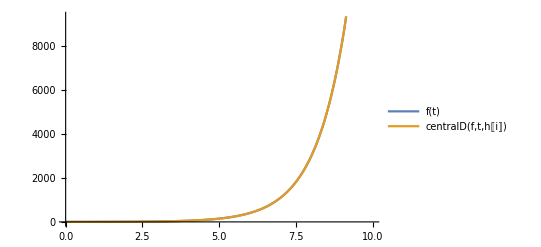
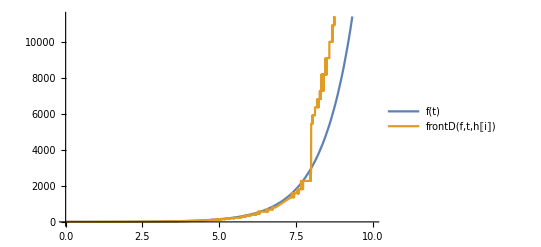
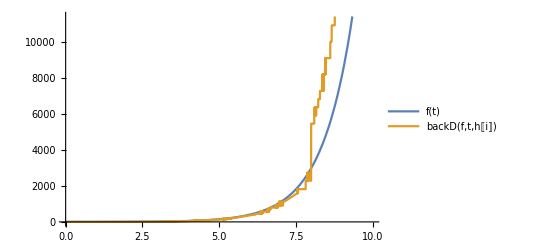

```mathematica
Table[{Plot[{f[t],frontD[f, t, h[[i]]]} ,{t,0,10}, PlotLegends->"Expressions"],
               Plot[{f[t],backD[f, t, h[[i]]]} ,{t,0,10}, PlotLegends->"Expressions"],
               Plot[{f[t], centralD[f, t, h[[i]]]} ,{t,0,10}, PlotLegends->"Expressions"]
}, {i,1,3}]
```

```mathematica
exactErr[realF_, aproxF_,t_, h_ ]:=Module[
{},
realF[t]-aproxF[realF, t,h]
]
aproxErr[realF_, aproxF_,t_, h_ ]:=Module[
{},

(realF[t]-aproxF[realF, t,h])/realF[t]
]
```

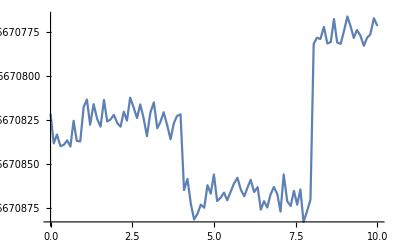
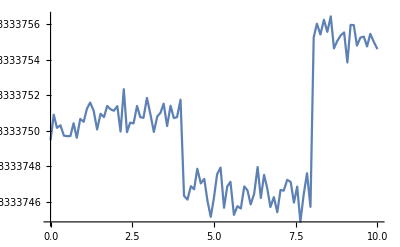
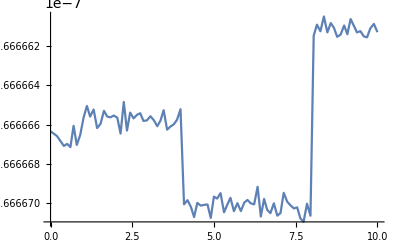
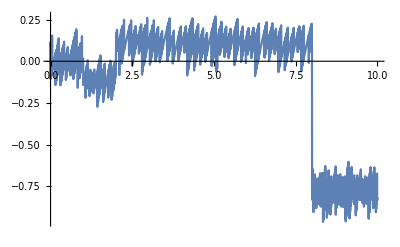
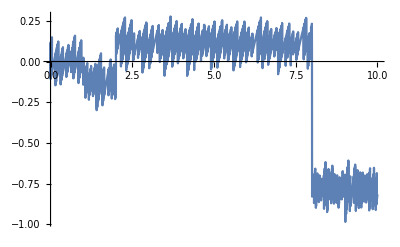
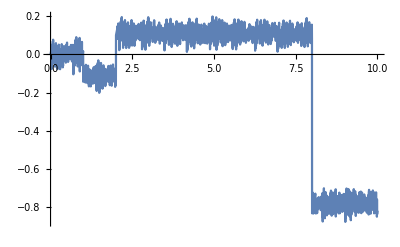
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[{
Plot[{{aproxErr[f,frontD, t, h[[i]]]}},{t,0,10}],
Plot[{{aproxErr[f,backD, t, h[[i]]]}},{t,0,10}],
Plot[{{aproxErr[f,centralD, t, h[[i]]]}},{t,0,10}]
}, {i,1,3}]
```

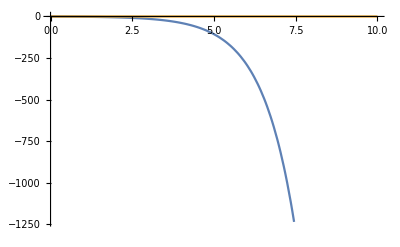
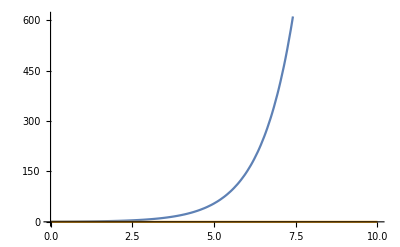
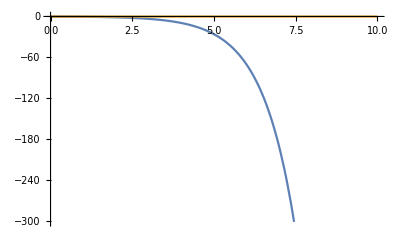
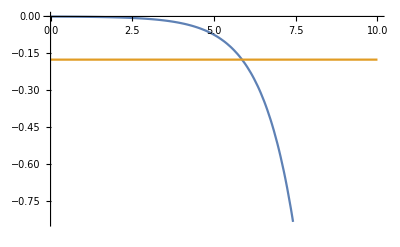
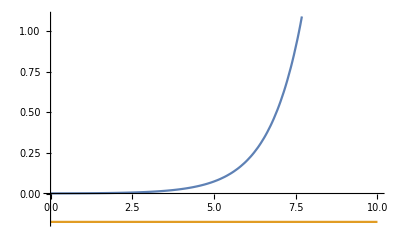
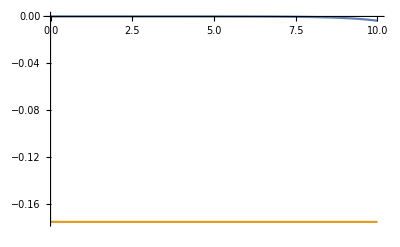
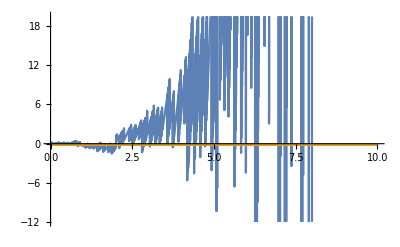
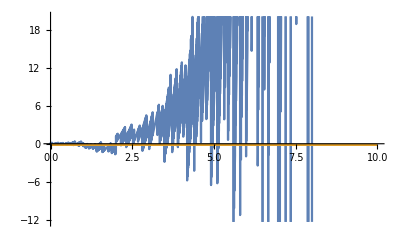

```mathematica
Table[{
Plot[{{exactErr[f,frontD, t, h[[i]]],aproxErr[f,centralD, t, Subscript[h, 1]]}},{t,0,10}],
Plot[{{exactErr[f,backD, t, h[[i]]],aproxErr[f,centralD, t, Subscript[h, 1]]}},{t,0,10}],
Plot[{{exactErr[f,centralD, t, h[[i]]],aproxErr[f,centralD, t, Subscript[h, 1]]}},{t,0,10}]
}, {i,1,3}]
```

```mathematica
f[x_]:=Cos[x]Sin[x]x
f1=Table[Normal[Series[f[x], {x, 5, n}]//N],{n, 1,100}];
```

```mathematica
Animate[
Plot[{f[t],f1[[i]]/.x->t},{t,0,10},PlotLegends->"Expressions",PlotRange->20 ],
{i,1,30, 1},AnimationRate->1
]
```

```mathematica
t = Table[x, {x,0,10,0.01}];
isT = False;
For[i = 1, !isT&&i<100, i++,
isT= True;
For[j = 1,isT&&j≤Length[t], j++,
If[
Abs[(f1[[i]]/.x->t[[j]])-f[t[[j]]]]>0.1,
isT=False;
];
];
If[isT, Print[i]
];
]
```

28